# AOE Thin-Wall Project

Group 7 - Don’t call my name, Don’t call my name, Mariko. That’s not my name, That’s not my name, Manana Got-no-man (Aesthetics), Vyon Coetzer, David Del Grosso, David Gardiner, Gaurav Sakhawala, Ronak Shah

Iteration 3: Stringers at each Corner

```mathematica
ClearAll["Global`*"]
```

ClearAll::wrsym: Symbol θR is Protected.

## Constants

```mathematica
ClearAll["Global`*"]
tf = .075;
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.04666 chord[x];*)(*box height (ft)*)
heightL[x_]=.04666*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.04666*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.04666*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.04666*chordR[x];*)

JL[x_]=1/3 widthL[x] heightL[x]^3; (*torsion constant 0≤x<27.5*)
JR[x_]=1/3 widthR[x] heightR[x]^3;(*torsion constant 27.5≤x<95.8*)
GCF=104427171.365; (*psf*)

Cm=.016;(*moment coefficient at 11 degree AoA*)

e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=3.1; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.15; (*radius of stringer ft*)
r2 = 0.15;
ASL=π*r^2;
ASR= Pi*r2^2;

tL[x_]=tf*heightR[x];
tR[x_]=tf*heightR[x];

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbs)*)

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

AwebL[x_]=tL[x]*(heightL[x]-2*tL[x]);
AwebR[x_]=tR[x]*(heightR[x]-2*tR[x]);


IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2+1/12*tL[x]*(heightL[x]-2*tL[x])^3*2+2*AwebL[x]*((widthL[x]-4tL[x])/6+tL[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2+1/12*(heightL[x]-2*tL[x])*tL[x]^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2+1/12*tR[x]*(heightR[x]-2*tR[x])^3*2+2*AwebR[x]*((widthR[x]-4tR[x])/6+tR[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2+1/12*(heightR[x]-2*tR[x])*tR[x]^3;(*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall ;(*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=1461980399.11; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;
Wtail=8360;
Cost = Wspar*10; (*material cost for spar in $ *)
WC = Wspar/Cost; (*Weight/Cost*)
```

ClearAll::wrsym: Symbol θR is Protected.

## Case 1 (Takeoff)

### Lift

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL;
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR;

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;


rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg];
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x];
```

### Torsion

Set::write: Tag θR in θR[x_] is Protected.

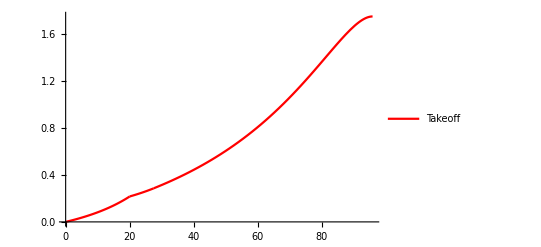

```mathematica
MtL[x_]=1/2 ρ Vto^2 S chordL[x]Cm+c20a;
MtM[x_]=1/2 ρ Vto^2 S chordL[x]Cm+c21a;
MtR[x_]=1/2 ρ Vto^2 S chordR[x]Cm+c22a;

ϕL[x_]=Integrate[1/(GCF JL[x])MtL[x],x]+c23a;
ϕM[x_]=Integrate[1/(GCF JL[x])MtM[x],x]+c24a;
ϕR[x_]=Integrate[1/(GCF JR[x])MtR[x],x]+c25a;


eq20a=ϕL[0]==0;
eq21a=ϕL[Leng]==ϕM[Leng];
eq22a=ϕM[27.5]==ϕR[27.5];
eq23a=MtR[95.8]==0;
eq24a=MtL[Leng]+Leng*18.5-T*3==MtM[Leng];
eq25a=MtM[27.5]==MtR[27.5];

sol3a=Solve[{eq20a,eq21a,eq22a,eq23a,eq24a,eq25a},{c20a,c21a,c22a,c23a,c24a,c25a}];
c20a=c20a/.sol3a[[1]];
c21a=c21a/.sol3a[[1]];
c22a=c22a/.sol3a[[1]];
c23a=c23a/.sol3a[[1]];
c24a=c24a/.sol3a[[1]];
c25a=c25a/.sol3a[[1]];


maxdistL[x_]=√((heightL[x]/2)^2+(widthL[x]/2)^2);
maxdistR[x_]=√((heightR[x]/2)^2+(widthR[x]/2)^2);
θL[x_]=ArcTan[(heightL[x]/2)/(widthL[x]/2)];
θR[x_]=ArcTan[(heightR[x]/2)/(widthR[x]/2)];

σxθLa[x_]=(MtL[x] maxdistL[x])/JL[x];
σxθMa[x_]=(MtM[x]maxdistL[x])/JL[x];
σxθRa[x_]=(MtR[x]maxdistR[x])/JR[x];

(*plot4=Plot[σxθLa[x],{x,0,Leng},PlotStyle->Red];
plot5=Plot[σxθMa[x],{x,Leng,27.5},PlotStyle->Blue];
plot6=Plot[σxθRa[x],{x,27.5,95.8},PlotStyle->Orange];
Show[{plot4,plot5,plot6},PlotRange->Automatic,AxesOrigin->{0,0}]

plot7=Plot[MtL[x],{x,0,Leng},PlotStyle->Red];
plot8=Plot[MtM[x],{x,Leng,27.5},PlotStyle->Blue];
plot9=Plot[MtR[x],{x,27.5,95.8},PlotStyle->Orange];
Show[{plot7,plot8,plot9},PlotRange->Automatic,AxesOrigin->{0,0}]*)

plot1a=Plot[180/π ϕL[x],{x,0,Leng},PlotStyle->Red,PlotLegends->{"Takeoff"}];
plot2a=Plot[180/π ϕM[x],{x,Leng,27.5},PlotStyle->Red];
plot3a=Plot[180/π ϕR[x],{x,27.5,95.8},PlotStyle->Red];
Show[{plot1a,plot2a,plot3a},PlotRange->Automatic,AxesOrigin->{0,0}]
Protect[plot1a];
Protect[plot2a];
Protect[plot3a];
Protect[σxθLa,σxθMa,σxθRa,θL,θR];
```

### Drag

```mathematica
pzL[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzM[x_]=Integrate[-pzM[x],x]+c2b;
VzR[x_]=Integrate[-pzR[x],x]+c3b;

MyL[x_]=Integrate[VzL[x],x]+c4b;
MyM[x_]=Integrate[VzM[x],x]+c5b;
MyR[x_]=Integrate[VzR[x],x]+c6b;

rotzL[x_]=Integrate[-MyL[x]/(EE IyyL[x]),x]+c7b;
rotzM[x_]=Integrate[-MyM[x]/(EE IyyL[x]),x]+c8b;
rotzR[x_]=Integrate[-MyR[x]/(EE IyyR[x]),x]+c9b;

uzL[x_]=Integrate[rotzL[x],x]+c10b;
uzM[x_]=Integrate[rotzM[x],x]+c11b;
uzR[x_]=Integrate[rotzR[x],x]+c12b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzM[Leng];
eq6b=rotzM[Ltaper]==rotzR[Ltaper];
eq7b=uzL[Leng]==uzM[Leng];
eq8b=uzM[Ltaper]==uzR[Ltaper];
eq9b=MyL[Leng]==MyM[Leng];
eq10b=MyM[Ltaper]==MyR[Ltaper];
eq11b=VzL[Leng]+T==VzM[Leng];
eq12b=VzM[Ltaper]==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b,eq9b,eq10b,eq11b,eq12b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b,c9b,c10b,c11b,c12b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];
c9b=c9b/.sol1b[[1]];
c10b=c10b/.sol1b[[1]];
c11b=c11b/.sol1b[[1]];
c12b=c12b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzM[x_]=pzM[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzM[x_]=VzM[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyM[x_]=MyM[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzM[x_]=rotzM[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzM[x_]=uzM[x];
uzR[x_]=uzR[x];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix … may contain significant numerical errors.

### Stress

```mathematica
σxxLa[x_] =Abs[ (MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1a[x_] = Abs[(MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2a[x_] = Abs[(MyM[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxRa[x_] = Abs[(MyR[x]*-widthR[x]/2)/IyyR[x]]+Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)

(*plt1 = Plot[σxxL[x],{x,0,Llg}];
plt2 = Plot[σxxM1[x],{x,Llg,Leng}];
plt3 = Plot[σxxM2[x],{x,Leng,27.5}];
plt4 = Plot[σxxR[x],{x,27.5,95.8}];

Show[{plt1,plt2,plt3,plt4},PlotRange->All,AxesOrigin->{0,0}]
σmax =σxxL[0];
uyR[95.8];*)

Protect[σxxLa,σxxM1a,σxxM2a,σxxRa];
```

```mathematica
(*num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,σxxM2[27.5,Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]*)
```

```mathematica
Show[%8935,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft (max) vs Location of Engine Case 1"],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Real is not a type of graphics.

Show[-0.00801586,AxesLabel→{Location of Engine (ft),Stress (Pa)},PlotLabel→Stress @ 27.5ft (max) vs Location of Engine Case 1,LabelStyle→{GrayLevel[0]}]

### Deflection

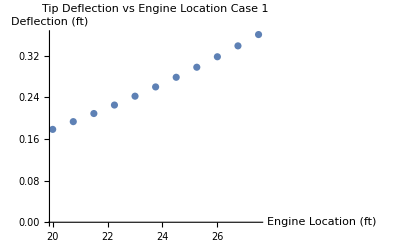

```mathematica
num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,uyRM[Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};

ListPlot[{data},PlotLabel->"Tip Deflection vs Engine Location Case 1",AxesLabel->{"Engine Location (ft)","Deflection (ft)"}]
```

### Overall Plots

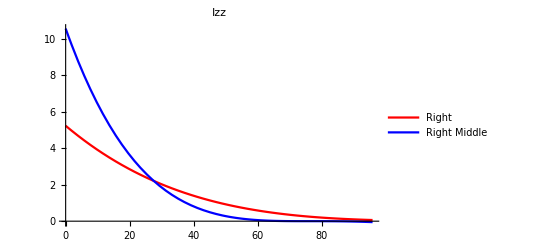

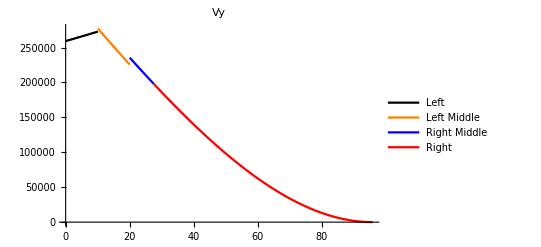

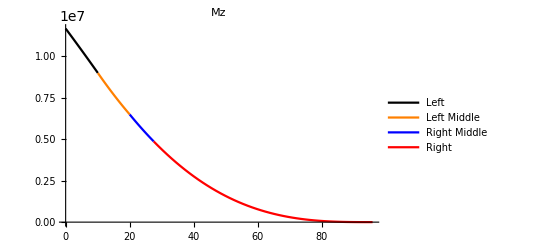

-Graphics-

-Graphics-

```mathematica
pl1=Plot[IzzR[x],{x,0,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
pl2=Plot[IzzL[x],{x,0,Lw},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
Show[{pl1,pl2},PlotRange->All,PlotLabel->"Izz",AxesOrigin->{0,0}]

pl3=Plot[VyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl4=Plot[VyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl5=Plot[VyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl6=Plot[VyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl3,pl4,pl5,pl6},PlotRange->All,PlotLabel->"Vy",AxesOrigin->{0,0}]

pl7=Plot[MzL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl8=Plot[MzLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl9=Plot[MzRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl10=Plot[MzR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl7,pl8,pl9,pl10},PlotRange->All,PlotLabel->"Mz",AxesOrigin->{0,0}]

pl11=Plot[rotyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl12=Plot[rotyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl13=Plot[rotyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl14=Plot[rotyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl11,pl12,pl13,pl14},PlotRange->All,PlotLabel->"roty",AxesOrigin->{0,0}]

pl15=Plot[uyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl16=Plot[uyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl17=Plot[uyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl18=Plot[uyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl15,pl16,pl17,pl18},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```

### Comments

```mathematica
(*tf={height/4,height/8,height/20,height/50,height/100};
Leng=20;
dataL=Transpose@{t,σxxR[27.5]};
(*Leng=(52.3+20)/2;
dataM=Transpose@{tf,σxx};
Leng=52.3;
dataR=Transpose@{t,σxx};
ListPlot[{dataL,dataM,dataR},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"}]*)
ListPlot[{dataL}]*)

(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]};
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]}*)
```

## Constants

```mathematica
ClearAll["Global`*"]
tf = .075;
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

AwebL[x_]=tL[x]*(heightL[x]-2*tL[x]);
AwebR[x_]=tR[x]*(heightR[x]-2*tR[x]);

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.04666 chord[x];*)(*box height (ft)*)
heightL[x_]=.04666*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.04666*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.04666*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.04666*chordR[x];*)

JL[x_]=1/3 widthL[x] heightL[x]^3; (*torsion constant 0≤x<27.5*)
JR[x_]=1/3 widthR[x] heightR[x]^3;(*torsion constant 27.5≤x<95.8*)
GCF=104427171.365; (*psf*)

Cm=.016;(*moment coefficient at 11 degree AoA*)


e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=3.1; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.15; (*radius of stringer ft*)
r2 = 0.15;
ASL=π*r^2;
ASR= Pi*r2^2;

tL[x_]=tf*heightR[x];
tR[x_]=tf*heightR[x];

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbs)*)

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2+1/12*tL[x]*(heightL[x]-2*tL[x])^3*2+2*AwebL[x]*((widthL[x]-4tL[x])/6+tL[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2+1/12*(heightL[x]-2*tL[x])*tL[x]^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2+1/12*tR[x]*(heightR[x]-2*tR[x])^3*2+2*AwebR[x]*((widthR[x]-4tR[x])/6+tR[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2+1/12*(heightR[x]-2*tR[x])*tR[x]^3;(*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=1461980399.11; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;
Wtail=8360;
Cost = Wspar*10; (*material cost for spar in $ *)
WC = Wspar/Cost; (*Weight/Cost*)
```

ClearAll::wrsym: Symbol plot1a is Protected.

ClearAll::wrsym: Symbol plot2a is Protected.

ClearAll::wrsym: Symbol plot3a is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

## Case 2 (Engine Failure)

### Lift

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
(*Lift  = (1/2 )*ρ35k*Vcruise^2*S*clmax*e;*)
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Wto/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]]; 
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[Ltaper]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[Ltaper]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[Ltaper]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[Ltaper]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg];
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x];

(*num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]*)
```

### Torsion

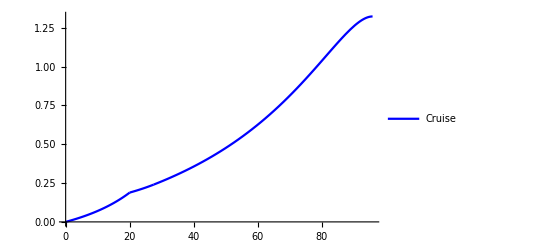

```mathematica
MtL[x_]=1/2 ρ35k Vcruise^2 S chordL[x]Cm+c20b;
MtM[x_]=1/2 ρ35k Vcruise^2 S chordL[x]Cm+c21b;
MtR[x_]=1/2 ρ35k Vcruise^2 S chordR[x]Cm+c22b;

ϕL[x_]=Integrate[1/(GCF JL[x])MtL[x],x]+c23b;
ϕM[x_]=Integrate[1/(GCF JL[x])MtM[x],x]+c24b;
ϕR[x_]=Integrate[1/(GCF JR[x])MtR[x],x]+c25b;


eq20b=ϕL[0]==0;
eq21b=ϕL[Leng]==ϕM[Leng];
eq22b=ϕM[27.5]==ϕR[27.5];
eq23b=MtR[95.8]==0;
eq24b=MtL[Leng]+Leng*18.5-T*3==MtM[Leng];
eq25b=MtM[27.5]==MtR[27.5];

sol3a=Solve[{eq20b,eq21b,eq22b,eq23b,eq24b,eq25b},{c20b,c21b,c22b,c23b,c24b,c25b}];
c20b=c20b/.sol3a[[1]];
c21b=c21b/.sol3a[[1]];
c22b=c22b/.sol3a[[1]];
c23b=c23b/.sol3a[[1]];
c24b=c24b/.sol3a[[1]];
c25b=c25b/.sol3a[[1]];

maxdistL[x_]=√((heightL[x]/2)^2+(widthL[x]/2)^2);
maxdistR[x_]=√((heightR[x]/2)^2+(widthR[x]/2)^2);

σxθLb[x_]=(MtL[x] maxdistL[x])/JL[x];
σxθMb[x_]=(MtM[x]maxdistL[x])/JL[x];
σxθRb[x_]=(MtR[x]maxdistR[x])/JR[x];

(*plot4=Plot[σxθL[x],{x,0,Leng},PlotStyle->Red];
plot5=Plot[σxθM[x],{x,Leng,27.5},PlotStyle->Blue];
plot6=Plot[σxθR[x],{x,27.5,95.8},PlotStyle->Orange];
Show[{plot4,plot5,plot6},PlotRange->Automatic,AxesOrigin->{0,0}]*)

plot1b=Plot[180/π ϕL[x],{x,0,Leng},PlotStyle->Blue,PlotLegends->{"Cruise"}];
plot2b=Plot[180/π ϕM[x],{x,Leng,27.5},PlotStyle->Blue];
plot3b=Plot[180/π ϕR[x],{x,27.5,95.8},PlotStyle->Blue];
Show[{plot1b,plot2b,plot3b},PlotRange->Automatic]
Protect[plot1b];
Protect[plot2b];
Protect[plot3b];
Protect[σxθLb,σxθMb,σxθRb];
```

### Drag

```mathematica
pzL[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzM[x_]=Integrate[-pzM[x],x]+c2b;
VzR[x_]=Integrate[-pzR[x],x]+c3b;

MyL[x_]=Integrate[VzL[x],x]+c4b;
MyM[x_]=Integrate[VzM[x],x]+c5b;
MyR[x_]=Integrate[VzR[x],x]+c6b;

rotzL[x_]=Integrate[-MyL[x]/(EE IyyL[x]),x]+c7b;
rotzM[x_]=Integrate[-MyM[x]/(EE IyyL[x]),x]+c8b;
rotzR[x_]=Integrate[-MyR[x]/(EE IyyR[x]),x]+c9b;

uzL[x_]=Integrate[rotzL[x],x]+c10b;
uzM[x_]=Integrate[rotzM[x],x]+c11b;
uzR[x_]=Integrate[rotzR[x],x]+c12b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzM[Leng];
eq6b=rotzM[Ltaper]==rotzR[Ltaper];
eq7b=uzL[Leng]==uzM[Leng];
eq8b=uzM[Ltaper]==uzR[Ltaper];
eq9b=MyL[Leng]==MyM[Leng];
eq10b=MyM[Ltaper]==MyR[Ltaper];
eq11b=VzL[Leng]+T==VzM[Leng];
eq12b=VzM[Ltaper]==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b,eq9b,eq10b,eq11b,eq12b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b,c9b,c10b,c11b,c12b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];
c9b=c9b/.sol1b[[1]];
c10b=c10b/.sol1b[[1]];
c11b=c11b/.sol1b[[1]];
c12b=c12b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzM[x_]=pzM[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzM[x_]=VzM[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyM[x_]=MyM[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzM[x_]=rotzM[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzM[x_]=uzM[x];
uzR[x_]=uzR[x];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix … may contain significant numerical errors.

### Stress

```mathematica
σxxLb[x_] =Abs[ (MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1b[x_] = Abs[(MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2b[x_] = Abs[(MyM[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxRb[x_] = Abs[(MyR[x]*-widthR[x]/2)/IyyR[x]]+Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)

(*plt1 = Plot[σxxL[x,Leng],{x,0,10.06}];
plt2 = Plot[σxxM1[x,Leng],{x,10.06,Leng}];
plt3 = Plot[σxxM2[x,Leng],{x,Leng,27.5}];
plt4 = Plot[σxxR[x,Leng],{x,27.5,95.8}];

Show[{plt1,plt2,plt3,plt4},PlotRange->All,AxesOrigin->{0,0}];*)

num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,σxxM2[27.5,Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]

Protect[σxxLb,σxxM1b,σxxM2b,σxxRb];
```

-Graphics-

### Overall Plots

-Graphics-

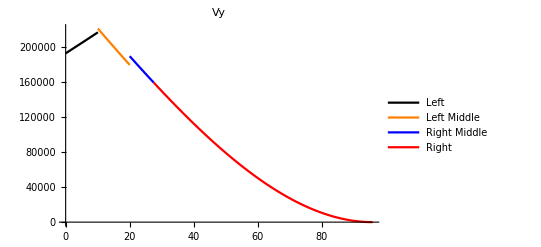

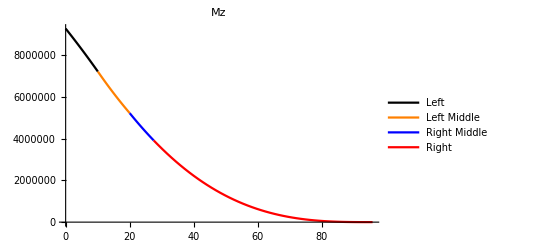

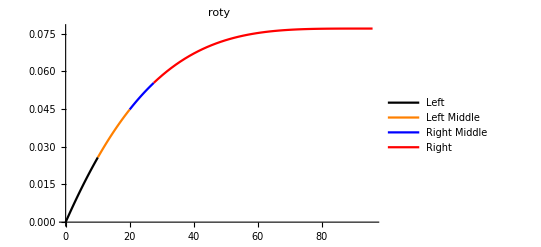

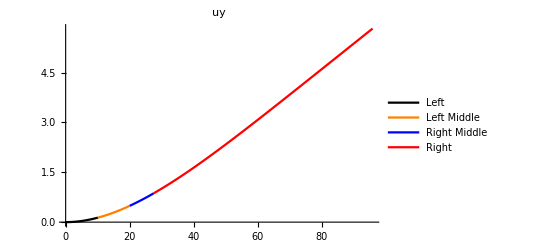

```mathematica
pl1=Plot[IzzR[x],{x,0,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
pl2=Plot[IzzL[x],{x,0,Lw},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
Show[{pl1,pl2},PlotRange->All,PlotLabel->"Izz",AxesOrigin->{0,0}]

pl3=Plot[VyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl4=Plot[VyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl5=Plot[VyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl6=Plot[VyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl3,pl4,pl5,pl6},PlotRange->All,PlotLabel->"Vy",AxesOrigin->{0,0}]

pl7=Plot[MzL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl8=Plot[MzLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl9=Plot[MzRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl10=Plot[MzR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl7,pl8,pl9,pl10},PlotRange->All,PlotLabel->"Mz",AxesOrigin->{0,0}]

pl11=Plot[rotyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl12=Plot[rotyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl13=Plot[rotyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl14=Plot[rotyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl11,pl12,pl13,pl14},PlotRange->All,PlotLabel->"roty",AxesOrigin->{0,0}]

pl15=Plot[uyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl16=Plot[uyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl17=Plot[uyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl18=Plot[uyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl15,pl16,pl17,pl18},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```

### Comments

```mathematica
(*Show[%8017,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Deflection ft]},PlotLabel->HoldForm[Tip Deflection ft vs Location of Engine ft Case 2],LabelStyle->{GrayLevel[0]}]*)
```

```mathematica
Show[%8086,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress at 27.5ft Max vs Engine Location Case 2"],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: BoxForm`AbsoluteRawBoxes is not a type of graphics.

Show[General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.,AxesLabel→{Location of Engine (ft),Stress (Pa)},PlotLabel→Stress at 27.5ft Max vs Engine Location Case 2,LabelStyle→{GrayLevel[0]}]

```mathematica
maxLeng=Solve[T*(Leng+Rfuse)== 5390000/FS,Leng];
maxLeng=Leng/.maxLeng[[1]];
```

Solve::ivar: 20 is not a valid variable.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
σxxR[27.5,20]
```

σxxR[27.5,20]

## Constants

```mathematica
ClearAll["Global`*"]
tf = .075;
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.04666 chord[x];*)(*box height (ft)*)
heightL[x_]=.04666*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.04666*chordR[x];
widthR[x_]=.65*chordR[x];

AwebL[x_]=tL[x]*(heightL[x]-2*tL[x]);
AwebR[x_]=tR[x]*(heightR[x]-2*tR[x]);
JL[x_]=1/3 widthL[x] heightL[x]^3; (*torsion constant 0≤x<27.5*)
JR[x_]=1/3 widthR[x] heightR[x]^3;(*torsion constant 27.5≤x<95.8*)
GCF=104427171.365; (*psf*)

Cm=.016;(*moment coefficient at 11 degree AoA*)

(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.04666*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.04666*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=3.1; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.15; (*radius of stringer ft*)
r2 = 0.15;
ASL=π*r^2;
ASR= Pi*r2^2;

tL[x_]=tf*heightR[x];
tR[x_]=tf*heightR[x];

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbs)*)

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2+1/12*tL[x]*(heightL[x]-2*tL[x])^3*2+2*AwebL[x]*((widthL[x]-4tL[x])/6+tL[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2+1/12*(heightL[x]-2*tL[x])*tL[x]^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2+1/12*tR[x]*(heightR[x]-2*tR[x])^3*2+2*AwebR[x]*((widthR[x]-4tR[x])/6+tR[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2+1/12*(heightR[x]-2*tR[x])*tR[x]^3;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=1461980399.11; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;
Wtail=8360;
Cost = Wspar*10;(*material cost for spar in $ *)
WC = Wspar/Cost;(*Weight/Cost*)
```

ClearAll::wrsym: Symbol plot1a is Protected.

ClearAll::wrsym: Symbol plot1b is Protected.

ClearAll::wrsym: Symbol plot2a is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

## Case 3 (Static)

### Lift

```mathematica
a=17.58; b=22.85; c=53.27; d=74.63;
 e=93.18; f=118.32; g=144.42; h=156.11; i=164.20;
sol3a=Solve[0== -Wto*(67)+2*Flg*(e-a),Flg]
Flg=Flg/.sol3a[[1]];
Fng=Wto-2*Flg;
```

{{Flg→243717.}}

```mathematica
(* distributed load *)
py[x_]=0;
PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL;
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASL;

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[Ltaper]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[Ltaper]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[Ltaper]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[Ltaper]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg]+Flg;
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x];
```

### Torsion

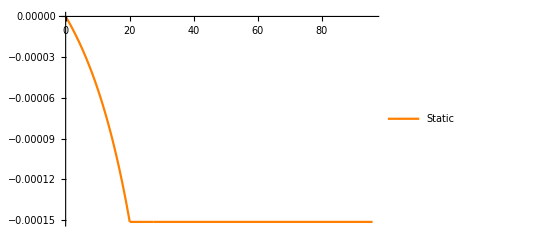

```mathematica
MtL[x_]=c20c;
MtM[x_]=c21c;
MtR[x_]=c22c;

ϕL[x_]=Integrate[1/(GCF JL[x])MtL[x],x]+c23c;
ϕM[x_]=Integrate[1/(GCF JL[x])MtM[x],x]+c24c;
ϕR[x_]=Integrate[1/(GCF JR[x])MtR[x],x]+c25c;


eq20c=ϕL[0]==0;
eq21c=ϕL[Leng]==ϕM[Leng];
eq22c=ϕM[27.5]==ϕR[27.5];
eq23c=MtR[95.8]==0;
eq24c=MtL[Leng]+Leng*18.5==MtM[Leng];
eq25c=MtM[27.5]==MtR[27.5];

sol3a=Solve[{eq20c,eq21c,eq22c,eq23c,eq24c,eq25c},{c20c,c21c,c22c,c23c,c24c,c25c}];
c20c=c20c/.sol3a[[1]];
c21c=c21c/.sol3a[[1]];
c22c=c22c/.sol3a[[1]];
c23c=c23c/.sol3a[[1]];
c24c=c24c/.sol3a[[1]];
c25c=c25c/.sol3a[[1]];

maxdistL[x_]=√((heightL[x]/2)^2+(widthL[x]/2)^2);
maxdistR[x_]=√((heightR[x]/2)^2+(widthR[x]/2)^2);

σxθLc[x_]=(MtL[x] maxdistL[x])/JL[x];
σxθMc[x_]=(MtM[x]maxdistL[x])/JL[x];
σxθRc[x_]=(MtR[x]maxdistR[x])/JR[x];

(*plot4=Plot[σxθL[x],{x,0,Leng},PlotStyle->Red];
plot5=Plot[σxθM[x],{x,Leng,27.5},PlotStyle->Blue];
plot6=Plot[σxθR[x],{x,27.5,95.8},PlotStyle->Orange];
Show[{plot4,plot5,plot6},PlotRange->Automatic,AxesOrigin->{0,0}]*)

plot1c=Plot[180/π ϕL[x],{x,0,Leng},PlotStyle->Orange,PlotLegends->{"Static"}];
plot2c=Plot[180/π ϕM[x],{x,Leng,27.5},PlotStyle->Orange];
plot3c=Plot[180/π ϕR[x],{x,27.5,95.8},PlotStyle->Orange];
Show[{plot1c,plot2c,plot3c},PlotRange->Automatic]
Protect[plot1c];
Protect[plot2c];
Protect[plot3c];
Protect[σxθLc,σxθMc,σxθRc];
```

### Stress

```mathematica
σxxLc[x_] =Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1c[x_] =Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2c[x_] = Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxRc[x_] = Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)

Protect[σxxLc,σxxM1c,σxxM2c,σxxRc];
```

### Overall Plots

-Graphics-

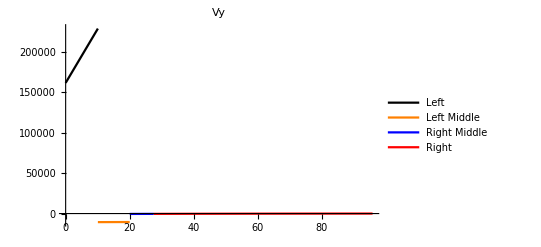

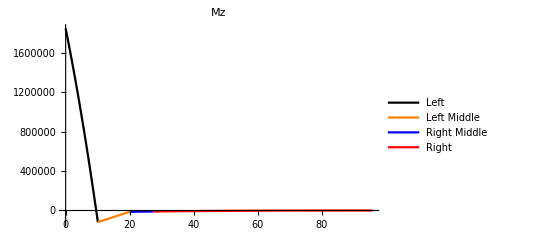

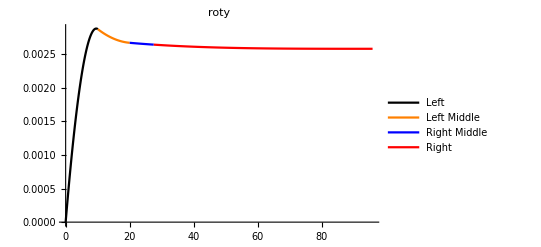

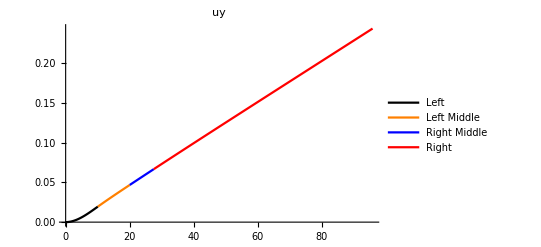

```mathematica
pl1=Plot[IzzR[x],{x,0,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
pl2=Plot[IzzL[x],{x,0,Lw},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
Show[{pl1,pl2},PlotRange->All,PlotLabel->"Izz",AxesOrigin->{0,0}]

pl3=Plot[VyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl4=Plot[VyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl5=Plot[VyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl6=Plot[VyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl3,pl4,pl5,pl6},PlotRange->All,PlotLabel->"Vy",AxesOrigin->{0,0}]

pl7=Plot[MzL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl8=Plot[MzLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl9=Plot[MzRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl10=Plot[MzR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl7,pl8,pl9,pl10},PlotRange->All,PlotLabel->"Mz",AxesOrigin->{0,0}]

pl11=Plot[rotyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl12=Plot[rotyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl13=Plot[rotyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl14=Plot[rotyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl11,pl12,pl13,pl14},PlotRange->All,PlotLabel->"roty",AxesOrigin->{0,0}]

pl15=Plot[uyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl16=Plot[uyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl17=Plot[uyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl18=Plot[uyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl15,pl16,pl17,pl18},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```

### Comments

```mathematica
(*Show[%8776,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft along Spar (max) vs Engine Location Case 3"],LabelStyle->{GrayLevel[0]}]*)
```

```mathematica
(*Show[%8772,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Tip Deflection ft]},PlotLabel->HoldForm[Tip Deflection vs Location of Engine Case 3],LabelStyle->{GrayLevel[0]}]*)
```

```mathematica
(*{{0.13248300656249998,-23.08462321638492},{0.06624150328124999,-11.603174462498314},{0.021197281049999996,11.884766836036333},{0.010598640524999998,41.998900299869774},{0.005299320262499999,101.14113311866477}}*)
```

```mathematica
(*num=(27.5-20)/10;*)
(*uvec={};Do[AppendTo[uvec,uyR[Leng ]],{Leng,20,27.5,num}]
data1=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data1] (*deflection at Leng*);*)


(*uvec2={};Do[AppendTo[uvec2,uyR[Lw]],{Leng,20,27.5,num}];
data2=Transpose@{Range[20,27.5,num],uvec2};
ListPlot[data2] (*deflection at Lw*)*)

(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]}
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]};
ListPlot[{data1,data2,data3},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"},PlotLabel->"Tip Deflection",AxesLabel->{"Thickness (ft)","Deflection (ft)"}]*)
```

```mathematica
(*num=(27.5-20)/10;*)
(*uvec3={};Do[AppendTo[uvec3,Abs[σxxM2[27.5,Leng]]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec3};
ListPlot[data]*)
```

## Graph

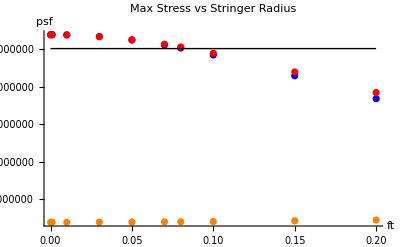

```mathematica
plot1=ListPlot[{{.0001,5.38209*10^6},{.1,4.83883*10^6},{.05,5.23625*10^6},{.2,3.67784*10^6},{.001,5.38203*10^6},{.01,5.37612*10^6},{.08,5.02254*10^6},{.07,5.10284*10^6},{.15,4.28541*10^6},{.03,5.32875*10^6}},PlotStyle->Blue];
plot2=ListPlot[{{.0001,5.37006*10^6},{.1,4.88631*10^6},{.05,5.24414*10^6},{.2,3.84093*10^6},{.001,5.37539*10^6},{.01,5.37006*10^6},{.08,5.05172*10^6},{.07,5.12402*10^6},{.15,4.38802*10^6},{.03,5.32742*10^6}},PlotStyle->Red];
plot3=ListPlot[{{.0001,391576},{.1,409992},{.05,396519},{.2,449373},{.001,391578},{.01,391778},{.08,403764},{.07,401042},{.15,428759},{.03,393384}},PlotStyle->Orange];
l1=Graphics@Line[{{0,5.0087*10^6},{.2,5.0087*10^6}}];
Show[{plot1,plot2,plot3,l1},PlotRange->All,PlotLabel->"Max Stress vs Stringer Radius",AxesLabel->{"ft","psf"},AxesOrigin->{0,0}]
```

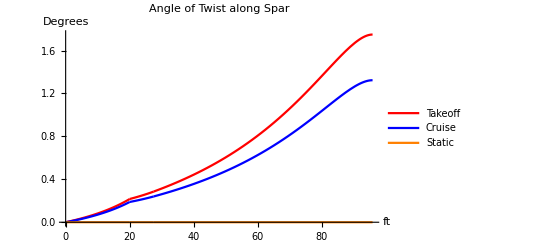

```mathematica
Unprotect[plot1a];
Unprotect[plot1b];
Unprotect[plot1c];
Unprotect[plot2a];
Unprotect[plot2b];
Unprotect[plot2c];
Unprotect[plot3a];
Unprotect[plot3b];
Unprotect[plot3c];
Show[{plot1a,plot2a,plot3a,plot1b,plot2b,plot3b,plot1c,plot2c,plot3c},PlotRange->All,PlotLabel->"Angle of Twist along Spar",AxesLabel->{"ft","Degrees"}]
```

## Stress

1.32866×10^6

1.32866×10^6

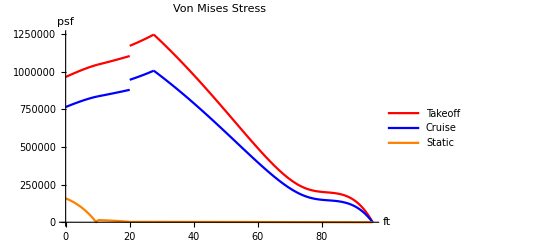

1.15731×10^6

920413.

158939.

```mathematica
Unprotect[σxxLa,σxxLb,σxxLc,σxxM1a,σxxM1b,σxxM1c,σxxM2a,σxxM2b,σxxM2c,σxxRa,σxxRb,,σxxRc,σxθLa,σxθLb,σxθLc,σxθMa,σxθMb,σxθMc,σxθRa,σxθRb,σxθRc,θL];

σxxLa[x_]=σxxLa[x];
σyyLa[x_]=σxθLa[x]Sin[θL[x]];
σzzLa[x_]=σxθLa[x]Cos[θL[x]];
σxyLa[x_]=0;
σxzLa[x_]=0;

σxxMLa[x_]=σxxM1a[x];
σyyMLa[x_]=σxθLa[x]Sin[θL[x]];
σzzMLa[x_]=σxθLa[x]Cos[θL[x]];
σxyMLa[x_]=0;
σxzMLa[x_]=0;

σxxMRa[x_]=σxxM2a[x];
σyyMRa[x_]=σxθMa[x]Sin[θL[x]];
σzzMRa[x_]=σxθMa[x]Cos[θL[x]];
σxyMRa[x_]=0;
σxzMRa[x_]=0;

σxxRa[x_]=σxxRa[x];
σyyRa[x_]=σxθRa[x]Sin[θR[x]];
σzzRa[x_]=σxθRa[x]Cos[θR[x]];
σxyRa[x_]=0;
σxzRa[x_]=0;

σMisesLa[x_]=√(1/2((σxxLa[x]-σyyLa[x])^2+(σyyLa[x]-σzzLa[x])^2+(σzzLa[x]-σxxLa[x])^2+6(σxyLa[x]^2+σxzLa[x]^2)));
σMisesMLa[x_]=√(1/2((σxxMLa[x]-σyyMLa[x])^2+(σyyMLa[x]-σzzMLa[x])^2+(σzzMLa[x]-σxxMLa[x])^2+6(σxyMLa[x]^2+σxzMLa[x]^2)));
σMisesMRa[x_]=√(1/2((σxxMRa[x]-σyyMRa[x])^2+(σyyMRa[x]-σzzMRa[x])^2+(σzzMRa[x]-σxxMRa[x])^2+6(σxyMRa[x]^2+σxzMRa[x]^2)));
σMisesRa[x_]=√(1/2((σxxRa[x]-σyyRa[x])^2+(σyyRa[x]-σzzRa[x])^2+(σzzRa[x]-σxxRa[x])^2+6(σxyRa[x]^2+σxzRa[x]^2)));

σxxLb[x_]=σxxLb[x];
σyyLb[x_]=σxθLb[x]Sin[θL[x]];
σzzLb[x_]=σxθLb[x]Cos[θL[x]];
σxyLb[x_]=0;
σxzLb[x_]=0;

σxxMLb[x_]=σxxM1b[x];
σyyMLb[x_]=σxθLb[x]Sin[θL[x]];
σzzMLb[x_]=σxθLb[x]Cos[θL[x]];
σxyMLb[x_]=0;
σxzMLb[x_]=0;

σxxMRb[x_]=σxxM2b[x];
σyyMRb[x_]=σxθMb[x]Sin[θL[x]];
σzzMRb[x_]=σxθMb[x]Cos[θL[x]];
σxyMRb[x_]=0;
σxzMRb[x_]=0;

σxxRb[x_]=σxxRb[x];
σyyRb[x_]=σxθRb[x]Sin[θR[x]];
σzzRb[x_]=σxθRb[x]Cos[θR[x]];
σxyRb[x_]=0;
σxzRb[x_]=0;

σMisesLb[x_]=√(1/2((σxxLb[x]-σyyLb[x])^2+(σyyLb[x]-σzzLb[x])^2+(σzzLb[x]-σxxLb[x])^2+6(σxyLb[x]^2+σxzLb[x]^2)));
σMisesMLb[x_]=√(1/2((σxxMLb[x]-σyyMLb[x])^2+(σyyMLb[x]-σzzMLb[x])^2+(σzzMLb[x]-σxxMLb[x])^2+6(σxyMLb[x]^2+σxzMLb[x]^2)));
σMisesMRb[x_]=√(1/2((σxxMRb[x]-σyyMRb[x])^2+(σyyMRb[x]-σzzMRb[x])^2+(σzzMRb[x]-σxxMRb[x])^2+6(σxyMRb[x]^2+σxzMRb[x]^2)));
σMisesRb[x_]=√(1/2((σxxRb[x]-σyyRb[x])^2+(σyyRb[x]-σzzRb[x])^2+(σzzRb[x]-σxxRb[x])^2+6(σxyRb[x]^2+σxzRb[x]^2)));

σxxLc[x_]=σxxLc[x];
σyyLc[x_]=σxθLc[x]Sin[θL[x]];
σzzLc[x_]=σxθLc[x]Cos[θL[x]];
σxyLc[x_]=0;
σxzLc[x_]=0;

σxxMLc[x_]=σxxM1c[x];
σyyMLc[x_]=σxθLc[x]Sin[θL[x]];
σzzMLc[x_]=σxθLc[x]Cos[θL[x]];
σxyMLc[x_]=0;
σxzMLc[x_]=0;

σxxMRc[x_]=σxxM2c[x];
σyyMRc[x_]=σxθMc[x]Sin[θL[x]];
σzzMRc[x_]=σxθMc[x]Cos[θL[x]];
σxyMRc[x_]=0;
σxzMRc[x_]=0;

σxxRc[x_]=σxxRc[x];
σyyRc[x_]=σxθRc[x]Sin[θR[x]];
σzzRc[x_]=σxθRc[x]Cos[θR[x]];
σxyRc[x_]=0;
σxzRc[x_]=0;


σMisesLc[x_]=√(1/2((σxxLc[x]-σyyLc[x])^2+(σyyLc[x]-σzzLc[x])^2+(σzzLc[x]-σxxLc[x])^2+6(σxyLc[x]^2+σxzLc[x]^2)));
σMisesMLc[x_]=√(1/2((σxxMLc[x]-σyyMLc[x])^2+(σyyMLc[x]-σzzMLc[x])^2+(σzzMLc[x]-σxxMLc[x])^2+6(σxyMLc[x]^2+σxzMLc[x]^2)));
σMisesMRc[x_]=√(1/2((σxxMRc[x]-σyyMRc[x])^2+(σyyMRc[x]-σzzMRc[x])^2+(σzzMRc[x]-σxxMRc[x])^2+6(σxyMRc[x]^2+σxzMRc[x]^2)));
σMisesRc[x_]=√(1/2((σxxRc[x]-σyyRc[x])^2+(σyyRc[x]-σzzRc[x])^2+(σzzRc[x]-σxxRc[x])^2+6(σxyRc[x]^2+σxzRc[x]^2)));
σxxMRa[27.5]
σxxRa[27.5]

plot1a=Plot[σMisesLa[x],{x,0,Llg},PlotStyle->Red,PlotLegends->{"Takeoff"}];
plot2a=Plot[σMisesMLa[x],{x,Llg,Leng},PlotStyle->Red];
plot3a=Plot[σMisesMRa[x],{x,Leng,27.5},PlotStyle->Red];
plot4a=Plot[σMisesRa[x],{x,27.5,95.8},PlotStyle->Red];
plot1b=Plot[σMisesLb[x],{x,0,Llg},PlotStyle->Blue,PlotLegends->{"Cruise"}];
plot2b=Plot[σMisesMLb[x],{x,Llg,Leng},PlotStyle->Blue];
plot3b=Plot[σMisesMRb[x],{x,Leng,27.5},PlotStyle->Blue];
plot4b=Plot[σMisesRb[x],{x,27.5,95.8},PlotStyle->Blue];
plot1c=Plot[σMisesLc[x],{x,0,Llg},PlotStyle->Orange,PlotLegends->{"Static"}];
plot2c=Plot[σMisesMLc[x],{x,Llg,Leng},PlotStyle->Orange];
plot3c=Plot[σMisesMRc[x],{x,Leng,27.5},PlotStyle->Orange];
plot4c=Plot[σMisesRc[x],{x,27.5,95.8},PlotStyle->Orange];
Show[{plot1a,plot2a,plot3a,plot4a,plot1b,plot2b,plot3b,plot4b,plot1c,plot2c,plot3c,plot4c},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Von Mises Stress",AxesLabel->{"ft","psf"}]

σMisesMLa[27.5]
σMisesMLb[27.5]
σMisesLc[0]
```

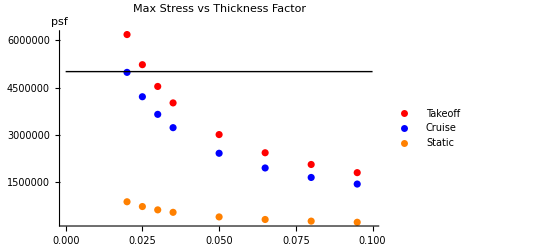

```mathematica
plot4=ListPlot[{{.05,3.013058232098722*10^6},{.065,2.43686*10^6},{.08,2.06493*10^6},{.095,1.80649*10^6},{.035,4.01671*10^6},{.02,6.18311*10^6},{.025,5.22811*10^6},{.03,4.53818*10^6}},PlotStyle->Red,PlotLegends->{"Takeoff"}];
plot5=ListPlot[{{.05,2.42046*10^6},{.065,1.95447*10^6},{.08,1.6537*10^6},{.095,1.44469*10^6},{.035,3.2322*10^6},{.02,4.9845*10^6},{.025,4.21203*10^6},{.03,3.65398*10^6}},PlotStyle->Blue,PlotLegends->{"Cruise"}];
plot6=ListPlot[{{.05,403202.36215962074},{.065,321860},{.08,270038},{.095,234212},{.035,548834},{.02,883485},{.025,732309},{.03,626728}},PlotStyle->Orange,PlotLegends->{"Static"}];

l2=Graphics@Line[{{0,5.0087*10^6},{.1,5.0087*10^6}}];
Show[{plot4,plot5,plot6,l2},PlotRange->All,PlotLabel->"Max Stress vs Thickness Factor",AxesLabel->{"","psf"},AxesOrigin->{0,0}]
```

## Fuselage (Static)

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,17.58,0.,0.,0.,0.,0.,0.,0.,3.27941×10^-10,0.,0.,0.,0.,0.,0.,0.,-1.92174×10^-9,-9.23434×10^-6},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,1.,-62566.1},«29»,{-1.,1.,0.,0.,0.,0.,0.,0.,-164.2,164.2,0.,0.,0.,0.,0.,0.,-2.86091×10^-8,2.86091×10^-8,0.,0.,0.,0.,0.,0.,1.56587×10^-6,-1.56587×10^-6,0.,0.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

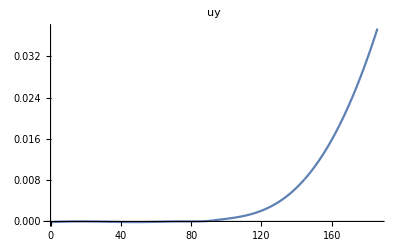

```mathematica
t=.1; ρAL=.1*(12/1)^3; EEAL=(144/1)10.2*10^6; Lf=186;
AF=π*((Rfuse+t)^2-(Rfuse)^2);
IyyF=IzzF=π/4((Rfuse+t)^4-(Rfuse)^4); pyF=2511.5; pyP=321.41;
(*-Graphics-*)
pyF1[x_]=-(AF*ρAL);
pyF2[x_]=-(AF*ρAL);
pyF3[x_]=-(AF*ρAL+pyP);
pyF4[x_]=-(AF*ρAL+pyP+pyF);
pyF5[x_]=-(AF*ρAL+pyP+pyF);
pyF6[x_]=-(AF*ρAL+pyP);
pyF7[x_]=-(AF*ρAL);
pyF8[x_]=-(AF*ρAL);
VyF1[x_]=Integrate[-pyF1[x],x]+c1f;
VyF2[x_]=Integrate[-pyF2[x],x]+c2f;
VyF3[x_]=Integrate[-pyF3[x],x]+c3f;
VyF4[x_]=Integrate[-pyF4[x],x]+c4f;
VyF5[x_]=Integrate[-pyF5[x],x]+c5f;
VyF6[x_]=Integrate[-pyF6[x],x]+c6f;
VyF7[x_]=Integrate[-pyF7[x],x]+c7f;
VyF8[x_]=Integrate[-pyF8[x],x]+c8f;
MzF1[x_]=Integrate[-VyF1[x],x]+c9f;
MzF2[x_]=Integrate[-VyF2[x],x]+c10f;
MzF3[x_]=Integrate[-VyF3[x],x]+c11f;
MzF4[x_]=Integrate[-VyF4[x],x]+c12f;
MzF5[x_]=Integrate[-VyF5[x],x]+c13f;
MzF6[x_]=Integrate[-VyF6[x],x]+c14f;
MzF7[x_]=Integrate[-VyF7[x],x]+c15f;
MzF8[x_]=Integrate[-VyF8[x],x]+c16f;
rotyF1[x_]=Integrate[MzF1[x]/(EEAL*IzzF),x]+c17f;
rotyF2[x_]=Integrate[MzF2[x]/(EEAL*IzzF),x]+c18f;
rotyF3[x_]=Integrate[MzF3[x]/(EEAL*IzzF),x]+c19f;
rotyF4[x_]=Integrate[MzF4[x]/(EEAL*IzzF),x]+c20f;
rotyF5[x_]=Integrate[MzF5[x]/(EEAL*IzzF),x]+c21f;
rotyF6[x_]=Integrate[MzF6[x]/(EEAL*IzzF),x]+c22f;
rotyF7[x_]=Integrate[MzF7[x]/(EEAL*IzzF),x]+c23f;
rotyF8[x_]=Integrate[MzF8[x]/(EEAL*IzzF),x]+c24f;
uyF1[x_]=Integrate[rotyF1[x],x]+c25f;
uyF2[x_]=Integrate[rotyF2[x],x]+c26f;
uyF3[x_]=Integrate[rotyF3[x],x]+c27f;
uyF4[x_]=Integrate[rotyF4[x],x]+c28f;
uyF5[x_]=Integrate[rotyF5[x],x]+c29f;
uyF6[x_]=Integrate[rotyF6[x],x]+c30f;
uyF7[x_]=Integrate[rotyF7[x],x]+c31f;
uyF8[x_]=Integrate[rotyF8[x],x]+c32f;
eqn1f=uyF1[a]== 0;
eqn2f=VyF1[a]== VyF2[a]+Fng;
eqn3f=VyF2[b]== VyF3[b];
eqn4f=VyF3[c]== VyF4[c];
eqn5f=VyF4[d]== VyF5[d]+2*VyL[0];
eqn6f=VyF5[c+croot]== VyF6[c+croot];
eqn7f=VyF6[g]== VyF7[g];
eqn8f=VyF7[i]+Wtail== VyF8[i];
eqn9f=rotyF1[a]== 0;
eqn10f=uyF4[d]== 0;
eqn11f=MzF1[a]== MzF2[a];
eqn12f=MzF2[b]== MzF3[b];
eqn13f=MzF3[c]== MzF4[c];
eqn14f=MzF4[d]== MzF5[d]+MtL[0];
eqn15f=MzF5[g]== MzF6[g];
eqn16f=MzF6[i]== MzF7[i];
eqn17f=MzF7[i]== MzF8[i];
eqn18f=rotyF4[d]== 0;
eqn19f=rotyF1[a]== rotyF2[a];
eqn20f=rotyF2[b]== rotyF3[b];
eqn21f=rotyF3[c]== rotyF4[c];
eqn22f=rotyF4[d]== rotyF5[d];
eqn23f=rotyF5[c+croot]== rotyF6[c+croot];
eqn24f=rotyF6[g]== rotyF7[g];
eqn25f=rotyF7[i]== rotyF8[i];
eqn26f=uyF1[a]== uyF2[a];
eqn27f=uyF2[b]== uyF3[b];
eqn28f=uyF3[c]== uyF4[c];
eqn29f=uyF4[d]== uyF5[d];
eqn30f=uyF5[c+croot]== uyF6[c+croot];
eqn31f=uyF6[g]== uyF7[g];
eqn32f=uyF7[i]== uyF8[i];
sol1f=Solve[{eqn1f,eqn2f,eqn3f,eqn4f,eqn5f,eqn6f,eqn7f,eqn8f,eqn9f,eqn10f,eqn11f,eqn12f,eqn13f,eqn14f,eqn15f,eqn16f,eqn17f,eqn18f,eqn19f,eqn20f,eqn21f,eqn22f,eqn23f,eqn24f,eqn25f,eqn26f,eqn27f,eqn28f,eqn29f,eqn30f,eqn31f,eqn32f},{c1f,c2f,c3f,c4f,c5f,c6f,c7f,c8f,c9f,c10f,c11f,c12f,c13f,c14f,c15f,c16f,c17f,c18f,c19f,c20f,c21f,c22f,c23f,c24f,c25f,c26f,c27f,c28f,c29f,c30f,c31f,c32f}];
c1f=c1f/.sol1f[[1]];
c2f=c2f/.sol1f[[1]];
c3f=c3f/.sol1f[[1]];
c4f=c4f/.sol1f[[1]];
c5f=c5f/.sol1f[[1]];
c6f=c6f/.sol1f[[1]];
c7f=c7f/.sol1f[[1]];
c8f=c8f/.sol1f[[1]];
c9f=c9f/.sol1f[[1]];
c10f=c10f/.sol1f[[1]];
c11f=c11f/.sol1f[[1]];
c12f=c12f/.sol1f[[1]];
c13f=c13f/.sol1f[[1]];
c14f=c14f/.sol1f[[1]];
c15f=c15f/.sol1f[[1]];
c16f=c16f/.sol1f[[1]];
c17f=c17f/.sol1f[[1]];
c18f=c18f/.sol1f[[1]];
c19f=c19f/.sol1f[[1]];
c20f=c20f/.sol1f[[1]];
c21f=c21f/.sol1f[[1]];
c22f=c22f/.sol1f[[1]];
c23f=c23f/.sol1f[[1]];
c24f=c24f/.sol1f[[1]];
c25f=c25f/.sol1f[[1]];
c26f=c26f/.sol1f[[1]];
c27f=c27f/.sol1f[[1]];
c28f=c28f/.sol1f[[1]];
c29f=c29f/.sol1f[[1]];
c30f=c30f/.sol1f[[1]];
c31f=c31f/.sol1f[[1]];
c32f=c32f/.sol1f[[1]];
plf1=Plot[uyF1[x],{x,0,a}];
plf2=Plot[uyF2[x],{x,a,b}];
plf3=Plot[uyF3[x],{x,b,c}];
plf4=Plot[uyF4[x],{x,c,d}];
plf5=Plot[uyF5[x],{x,d,c+croot}];
plf6=Plot[uyF6[x],{x,c+croot,g}];
plf7=Plot[uyF7[x],{x,g,i}];
plf8=Plot[uyF8[x],{x,i,Lf}];
Show[{plf1,plf2,plf3,plf4,plf5,plf6,plf7,plf8},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```